```mathematica
ClearAll
```

ClearAll

```mathematica
1+1
```

2

```mathematica
k=1;
n0=-10;
nf=1;
t0=-Exp[-n0];
tf=-Exp[-nf];
```

```mathematica
ζ[t_]=(1+ⅈ*k*t)*Exp[-ⅈ*k*t];
cζ[t_]:=(1-ⅈ*k*t)*Exp[ⅈ*k*t];
η[t_]:=1
```

```mathematica
s=NDSolve[{x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ζ[t]*y1[t]+D[cζ[t],t]*cζ[t]*y2[t]), x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ζ[t]*y1[t]+-D[ζ[t],t]*cζ[t]*y2[t]),y1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cζ[t]*x1[t]+-D[cζ[t],t]*cζ[t]*x2[t]),
y2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ζ[t]*x1[t]+D[cζ[t],t]*ζ[t]*x2[t]), x1[t0]==1, x2[t0]==0, y1[t0]==0, y2[t0]==0},{x1,x2,y1,y2},{t,t0,tf}]
```

{{x1→InterpolatingFunction[{{-22026.5, -0.367879}}, <>],x2→InterpolatingFunction[{{-22026.5, -0.367879}}, <>],y1→InterpolatingFunction[{{-22026.5, -0.367879}}, <>],y2→InterpolatingFunction[{{-22026.5, -0.367879}}, <>]}}

```mathematica
xx1[t_]:=x1[t]/.s
xx2[t_]:=x2[t]/.s
yy1[t_]:=y1[t]/.s
yy2[t_]:=y2[t]/.s
```

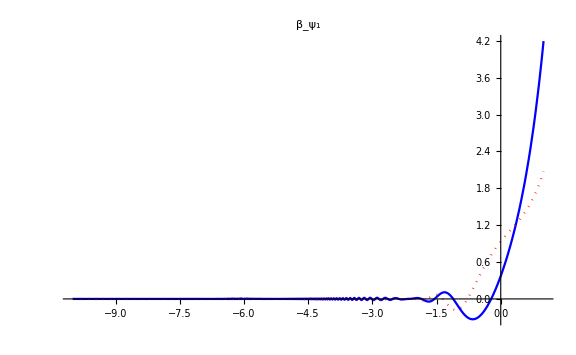

```mathematica
p4=ReImPlot[yy2[-Exp[-n]], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing, Red]}, PlotLabel->Subscript[β, Subscript[ψ, 1]],ImageSize->Large, PlotRange->All]
```

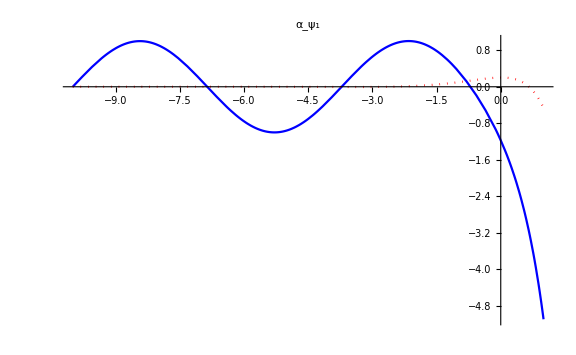

```mathematica
p3=ReImPlot[yy1[-Exp[-n]], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing, Red]}, PlotLabel->Subscript[α, Subscript[ψ, 1]], ImageSize->Large, PlotRange->All]
```

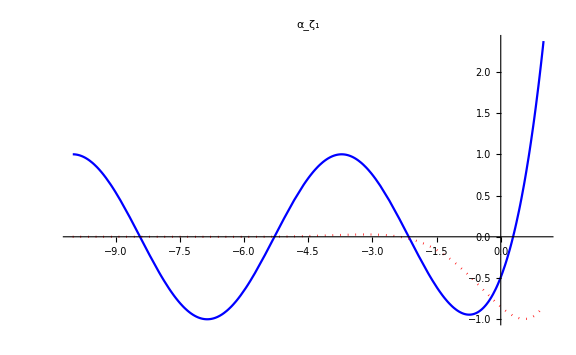

```mathematica
p1=ReImPlot[xx1[-Exp[-n]], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing, Red]}, PlotLabel->Subscript[α, Subscript[ζ, 1]], ImageSize->Large, PlotRange->All]
```

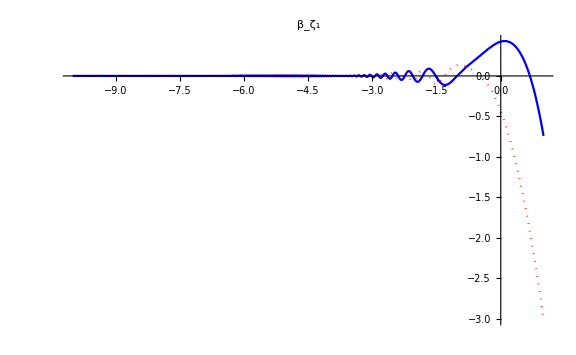

```mathematica
p2=ReImPlot[xx2[-Exp[-n]], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing, Red]}, PlotLabel->Subscript[β, Subscript[ζ, 1]], ImageSize->Large, PlotRange->All]
```

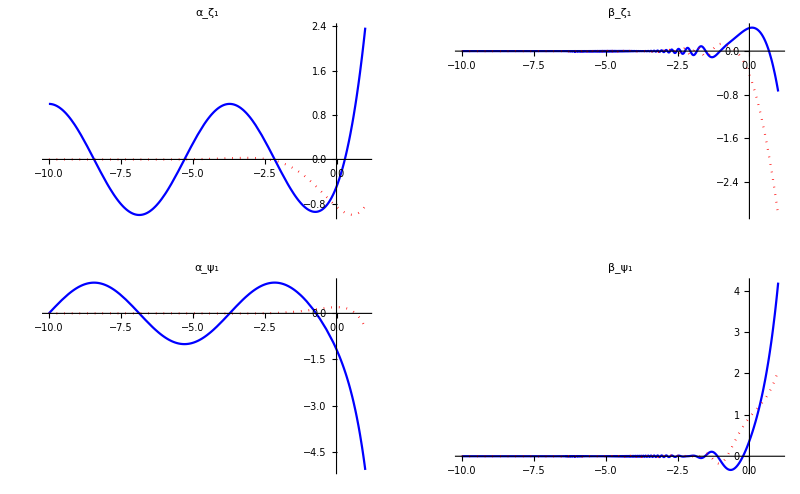

```mathematica
GraphicsGrid[{{p1,p2},{p3,p4}}, ImageSize->Full]
```